## Initializing

#### Candidate ranges

from findcriticaleigenvalues (other notebook). Found with ρinf = 20*λ. First three λcs sort of added in there.

```mathematica
ranges={{0.5,1.},{3.,4.},{6.5,7.5},{12.900390625,13.8671875},{19.66796875,20.634765625},{28.369140625,29.3359375},{39.00390625,39.970703125},{50.60546875,51.572265625},{64.140625,65.107421875},{78.642578125,79.609375},{96.044921875,97.01171875},{113.447265625,114.4140625},{133.75,134.716796875},{155.01953125,155.986328125},{178.22265625,179.189453125},{202.392578125,203.359375},{228.49609375,229.462890625},{255.56640625,256.533203125},{285.537109375,286.50390625},{315.5078125,316.474609375},{348.37890625,349.345703125},{382.216796875,383.18359375},{417.98828125,418.955078125},{454.7265625,455.693359375},{493.3984375,494.365234375},{533.037109375,534.00390625},{574.609375,575.576171875},{618.115234375,619.08203125},{663.5546875,664.521484375},{709.9609375,710.927734375},{757.333984375,758.30078125},{807.607421875,808.57421875},{858.84765625,859.814453125},{911.0546875,912.021484375},{965.1953125,966.162109375}};
```

#### Functions for finding λcs

This function pulls out the list of the 25 eigenvalues closest to zero. Around the lower lambdas, that is rough for bisection.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=consts[[2]];
nn=Round[consts[[3]]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

This one counts the negative eigenvalues at some λ.

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

This is a bisection routine. It tries to catch when eigenvalues fall off the end by checking to see whether the first eigenvalue at the high end of the range is lower than the first eigenvalue at the low end of the range. This usually means that one was lost.

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]),
Return[Bisect[F,consts,x0,mid,ϵ]];,
Return[Bisect[F,consts,mid,xf,ϵ]];
];,
Return[mid];
]
]
```

This function finds the lambda critical. I use this because I wanted to make sure I was bisecting a range with a root in it.

```mathematica
Findlc[input_,i_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,3]/3]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{input[[2]],40000,40000/input[[2]]}];
vah=Critical[input[[4]],{input[[2]],40000,40000/input[[2]]}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{input[[2]],20000,20000/input[[2]]},input[[3]],input[[4]],10^(-6)]};
Print[{{val[[1]],lnegs},{vah[[1]],hnegs},res}];
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

This will be needed later, for folding in recomputed values in the event of a range without a zero.

```mathematica
Merge[a_,b_]:=Module[{vals,res},
res=a;
vals=b;
For[i=1,i≤Length[res],i++,
If[res[[i,2]]==Null,(*if this was a recomputed value*)
res[[i]]=vals[[1]]; (*Slot in the head of the list of recomputed values*)
vals=Delete[vals,1]; (*and delete it, moving the next value to the head*)
];
];
Return[res]
]
```

#### Massaging inputs:

```mathematica
rhoinfs={0.1,0.05,0.025};
```

Making a list of inputs -- {number, ρinf, range low, range high}. Joins done in order to broaden some ranges.

```mathematica
inputs=Table[{11-j,0.01*j,ranges[[5,1]]-1,ranges[[5,2]]+1},{j,10,1,-1}]
```

{{1,0.1,18.668,21.6348},{2,0.09,18.668,21.6348},{3,0.08,18.668,21.6348},{4,0.07,18.668,21.6348},{5,0.06,18.668,21.6348},{6,0.05,18.668,21.6348},{7,0.04,18.668,21.6348},{8,0.03,18.668,21.6348},{9,0.02,18.668,21.6348},{10,0.01,18.668,21.6348}}

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs]
```

```mathematica
testlcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,10}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 1th lambda, part 2

***Beginning to calculate the 1th lambda, part 3

***Beginning to calculate the 2th lambda, part 4

***Beginning to calculate the 2th lambda, part 5

***Beginning to calculate the 2th lambda, part 6

***Beginning to calculate the 3th lambda, part 7

***Beginning to calculate the 3th lambda, part 8

***Beginning to calculate the 3th lambda, part 9

***Beginning to calculate the 4th lambda, part 10

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.4097

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.5951

Pass!

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7805

Pass!

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7791

Bisecting. Midpoint is 19.7805

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7783

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7791

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.778

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7783

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7778

Bisecting. Midpoint is 19.7791

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7787

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7778

Bisecting. Midpoint is 19.7783

Bisecting. Midpoint is 19.7789

Bisecting. Midpoint is 19.7774

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.778

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7778

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7783

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7777

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7778

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7782

{{6.15493×10^-9,0},{6.20971×10^-9,0},{3,19.7778}}

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7788

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7765

{{6.15491×10^-9,0},{6.20969×10^-9,0},{4,19.7773}}

{{6.15493×10^-9,0},{6.2097×10^-9,0},{1,19.7788}}

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7782

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.5951

{{6.15493×10^-9,0},{6.2097×10^-9,0},{2,19.7782}}

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7771

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7765

Bisecting. Midpoint is 19.777

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7764

Bisecting. Midpoint is 19.7767

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7764

{{6.15489×10^-9,0},{6.2097×10^-9,0},{7,19.7764}}

Bisecting. Midpoint is 19.777

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.777

Bisecting. Midpoint is 19.7767

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7758

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.776

{{6.1549×10^-9,0},{6.20969×10^-9,0},{5,19.7769}}

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7766

Bisecting. Midpoint is 19.7761

{{6.1549×10^-9,0},{6.2097×10^-9,0},{6,19.7766}}

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7761

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7761

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7758

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.776

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7761

Bisecting. Midpoint is 19.7762

{{6.15489×10^-9,0},{6.2097×10^-9,0},{8,19.7762}}

Bisecting. Midpoint is 19.776

Bisecting. Midpoint is 19.776

Bisecting. Midpoint is 19.776

«5 more identical outputs»

{{6.15489×10^-9,0},{6.2097×10^-9,0},{9,19.776}}

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7754

$Aborted

```mathematica
inputs=Table[{j,{0.1-(0.01*(j-1)),8000+(4000*(j-1))},ranges[[5,1]]-1,ranges[[5,2]]+1},{j,1,9}]
```

{{1,{0.1,8000},18.668,21.6348},{2,{0.09,12000},18.668,21.6348},{3,{0.08,16000},18.668,21.6348},{4,{0.07,20000},18.668,21.6348},{5,{0.06,24000},18.668,21.6348},{6,{0.05,28000},18.668,21.6348},{7,{0.04,32000},18.668,21.6348},{8,{0.03,36000},18.668,21.6348},{9,{0.02,40000},18.668,21.6348}}

```mathematica
Findlc[input_,i_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,3]/3]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{input[[2,1]],input[[2,2]],input[[2,2]]/input[[2,1]]}];
vah=Critical[input[[4]],{input[[2,1]],input[[2,2]],input[[2,2]]/input[[2,1]]}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{input[[2,1]],input[[2,2]],input[[2,2]]/input[[2,1]]},input[[3]],input[[4]],10^(-6)]};
Print[{{val[[1]],lnegs},{vah[[1]],hnegs},res}];
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Return[res]
]
```

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs]
```

```mathematica
testlcs2=ParallelTable[Findlc[inputs[[i]],i],{i,1,9}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 1th lambda, part 2

***Beginning to calculate the 1th lambda, part 3

***Beginning to calculate the 2th lambda, part 4

***Beginning to calculate the 2th lambda, part 5

***Beginning to calculate the 2th lambda, part 6

***Beginning to calculate the 3th lambda, part 7

***Beginning to calculate the 3th lambda, part 8

***Beginning to calculate the 3th lambda, part 9

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 20.1514

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.4097

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.8269

Bisecting. Midpoint is 19.8037

Bisecting. Midpoint is 19.9659

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7921

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.7863

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7892

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.8269

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7878

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7885

Bisecting. Midpoint is 19.8037

Bisecting. Midpoint is 19.7888

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7887

Bisecting. Midpoint is 19.7921

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7863

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7834

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.782

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7791

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7827

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7886

Bisecting. Midpoint is 19.7798

Bisecting. Midpoint is 19.7823

Bisecting. Midpoint is 19.7886

Pass!

Bisecting. Midpoint is 20.1514

{{1.5253×10^-7,0},{1.59466×10^-7,0},{1,19.7886}}

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7825

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7793

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7793

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7769

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7774

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7826

Bisecting. Midpoint is 19.6878

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.6878

{{6.80384×10^-8,0},{7.00826×10^-8,0},{2,19.7826}}

Bisecting. Midpoint is 19.7794

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.5951

{{3.83413×10^-8,0},{3.92015×10^-8,0},{3,19.7794}}

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7773

Bisecting. Midpoint is 19.7689

{{2.45654×10^-8,0},{2.50052×10^-8,0},{4,19.7773}}

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 19.7736

Bisecting. Midpoint is 19.7758

Bisecting. Midpoint is 19.6878

Bisecting. Midpoint is 19.7776

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.7738

Bisecting. Midpoint is 19.776

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7762

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7754

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7751

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.5951

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7749

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7739

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7759

Bisecting. Midpoint is 19.7739

{{1.70718×10^-8,0},{1.7326×10^-8,0},{5,19.7759}}

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.6878

{{9.61169×10^-9,0},{9.71882×10^-9,0},{7,19.7739}}

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7748

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 19.7342

Bisecting. Midpoint is 19.7748

{{1.25491×10^-8,0},{1.27091×10^-8,0},{6,19.7748}}

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7573

Bisecting. Midpoint is 19.774

Bisecting. Midpoint is 19.7736

Bisecting. Midpoint is 19.7689

Bisecting. Midpoint is 19.7735

Bisecting. Midpoint is 19.7734

Bisecting. Midpoint is 19.7747

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7718

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7733

«2 more identical outputs»

Bisecting. Midpoint is 19.7726

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7729

Bisecting. Midpoint is 19.7733

Bisecting. Midpoint is 19.7727

{{7.59676×10^-9,0},{7.67197×10^-9,0},{8,19.7733}}

Bisecting. Midpoint is 19.7728

Bisecting. Midpoint is 19.7728

Bisecting. Midpoint is 19.7728

«6 more identical outputs»

{{6.15489×10^-9,0},{6.2097×10^-9,0},{9,19.7728}}

{{1,19.7886},{2,19.7826},{3,19.7794},{4,19.7773},{5,19.7759},{6,19.7748},{7,19.7739},{8,19.7733},{9,19.7728}}

```mathematica
inputs=Table[{j,{0.1*2^(-(j-1)),1000},ranges[[5,1]]-1,ranges[[5,2]]+1},{j,1,6}]
```

{{1,{0.1,1000},18.668,21.6348},{2,{0.05,1000},18.668,21.6348},{3,{0.025,1000},18.668,21.6348},{4,{0.0125,1000},18.668,21.6348},{5,{0.00625,1000},18.668,21.6348},{6,{0.003125,1000},18.668,21.6348}}

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs]
```

```mathematica
testlcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,6}]
```

***Beginning to calculate the 1th lambda, part 1

***Beginning to calculate the 1th lambda, part 2

***Beginning to calculate the 1th lambda, part 3

***Beginning to calculate the 2th lambda, part 4

***Beginning to calculate the 2th lambda, part 5

***Beginning to calculate the 2th lambda, part 6

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.4097

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.7805

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.9196

Bisecting. Midpoint is 19.8964

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.4097

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.908

Bisecting. Midpoint is 19.9138

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.9109

Bisecting. Midpoint is 19.9123

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.9116

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9114

Bisecting. Midpoint is 19.9196

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.8964

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.908

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9138

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9196

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.9113

Bisecting. Midpoint is 19.9109

{{-0.00463758,1},{-0.000185076,1},{1,19.9113}}

Bisecting. Midpoint is 19.9094

Bisecting. Midpoint is 19.8964

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.9087

Bisecting. Midpoint is 19.908

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9093

Bisecting. Midpoint is 19.9138

Bisecting. Midpoint is 19.9092

Bisecting. Midpoint is 19.9109

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9094

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9087

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9196

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9091

Pass!

Bisecting. Midpoint is 20.1514

Bisecting. Midpoint is 19.9085

Bisecting. Midpoint is 19.8964

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.9091

Bisecting. Midpoint is 19.9086

{{-0.00464135,1},{-0.000185519,1},{2,19.9091}}

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.908

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.9138

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.9109

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.9086

Bisecting. Midpoint is 19.9094

Bisecting. Midpoint is 19.9086

{{-0.00464229,1},{-0.00018563,1},{3,19.9086}}

Bisecting. Midpoint is 19.9087

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.4097

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.9085

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.7805

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9196

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

{{-0.00464253,1},{-0.000185658,1},{4,19.9084}}

Bisecting. Midpoint is 19.8964

Bisecting. Midpoint is 19.9659

Bisecting. Midpoint is 19.908

Bisecting. Midpoint is 19.9138

Bisecting. Midpoint is 19.8732

Bisecting. Midpoint is 19.9109

Bisecting. Midpoint is 19.9094

Bisecting. Midpoint is 19.9196

Bisecting. Midpoint is 19.9087

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.8964

Bisecting. Midpoint is 19.9085

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.908

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9138

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9109

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9094

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9087

{{-0.00464258,1},{-0.000185665,1},{5,19.9084}}

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9085

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

Bisecting. Midpoint is 19.9084

«6 more identical outputs»

{{-0.0046426,1},{-0.000185667,1},{6,19.9084}}

{{1,19.9113},{2,19.9091},{3,19.9086},{4,19.9084},{5,19.9084},{6,19.9084}}

```mathematica
inputs
```

{{1,{0.1,1000},18.668,21.6348},{2,{0.05,1000},18.668,21.6348},{3,{0.025,1000},18.668,21.6348},{4,{0.0125,1000},18.668,21.6348},{5,{0.00625,1000},18.668,21.6348},{6,{0.003125,1000},18.668,21.6348}}

```mathematica
ns=Table[inputs[[i,2,2]]/inputs[[i,2,1]],{i,1,Length[inputs]}]
```

{10000.,20000.,40000.,80000.,160000.,320000.}

```mathematica
timing={35.545,77.980,124.527,241.134,985.831,1712.700}
```

{35.545,77.98,124.527,241.134,985.831,1712.7}

```mathematica
timingdata=Table[{ns[[i]],timing[[i]]},{i,1,6}]
```

{{10000.,35.545},{20000.,77.98},{40000.,124.527},{80000.,241.134},{160000.,985.831},{320000.,1712.7}}

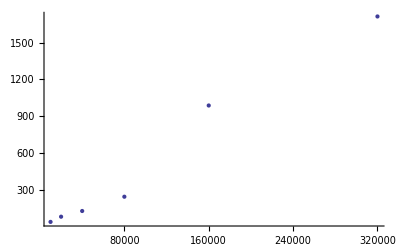

```mathematica
ListPlot[timingdata]
```

```mathematica
model=LinearModelFit[timingdata,x,x]
```

FittedModel[-64.8932+0.00566203 x]

```mathematica
model["RSquared"]
```

0.979202

```mathematica
Normal[model]
```

-64.8932+0.00566203 x

```mathematica
%75/.x->(1600000*2)
```

18053.6

```mathematica
%76/(60*60)
```

5.01489

```mathematica
%75/.x->(800000)
```

4464.73

```mathematica
%78/(60*60)
```

1.2402

```mathematica
4*%77+3*%79
```

23.7802

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+⋯ that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+⋯ where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.